## Práctica I

```mathematica
(* Definición de las Matrices de Pauli *)
sz={{1,0},{0,-1}};sp={{0,1},{0,0}};sm=Transpose[sp];sx=(sp+sm);sy=(sp-sm)/(I);s1[1]=sx;s1[2]=sy;s1[3]=sz;s1[4]={{1,0},{0,1}};s1[i_,j_]=KroneckerProduct[s1[i],s1[j]];
fs=FullSimplify;
mf=MatrixForm;
prod=KroneckerProduct;
id=IdentityMatrix;
s={sx,sy,sz};
daga=ConjugateTranspose;

(* Transpuesta parcial General *)
Clear[nu,nn,au,i,j];
ind[nu_,nn_]:={iaux=1+Floor[(nu-1)/nn],nu-(iaux-1)*nn};
rhotp[au_]:=(nn=Sqrt[Length[au]];
Table[{i,j}=ind[it,nn];{k,l}=ind[jt,nn];
au[[nn*(i-1)+l,nn*(k-1)+j]],{it,nn^2},{jt,nn^2}]); 

(* Base Estándar *)
(* Estados de la base estandar de un qubit *)
st0={1,0};st1={0,1};
(* Estados de la base {|+>,|->} de un qubit *)
stp=(st0+st1)/√2;stm=(st0-st1)/√2;

(* Estados de la base estandar de dos qubit *)
st00=Flatten[prod[st0,st0]];
st01=Flatten[prod[st0,st1]];
st10=Flatten[prod[st1,st0]];
st11=Flatten[prod[st1,st1]];



(* Proyectores en la Base Estándar *)

P0={{1,0},{0,0}};
P1={{0,0},{0,1}};

(* Proyectores en la {|+>,|->} *)

Pp=prod[stp,stp];
Pm=prod[stm,stm];

n[1]={1,0,0}; n[2]={0,1,0};n[3]={0,0,1};n[4]={1,0,1}/Sqrt[2];
σ={s1[1],s1[2],s1[3]};

(* Rotación General de un qubit *)

R[i_,θ_]=MatrixExp[-I θ n[i].σ/2] ;


Pm
```

{{1/2,-1/2},{-1/2,1/2}}

```mathematica
1)Para cada uno de los estados fı́sicos,calcule las probabilidades de obtener|0⟩ y|1⟩ cuando
se mide en la base estándar y cuando se mide en la base|±⟩=(|0⟩± |1⟩)/√2.
```

```mathematica
a)
```

```mathematica
sta=(st0+st1)/√2
```

{1/(√2),1/(√2)}

```mathematica
sta.sta
```

1

```mathematica
ConjugateTranspose[P0]
```

{{1,0},{0,0}}

```mathematica
P0.P0
```

{{1,0},{0,0}}

```mathematica
(*Probabilidad de obtener |0> y |1> midiendo en la base estándar *)
```

```mathematica
sta.P0.sta
```

1/2

```mathematica
sta.P1.sta
```

1/2

```mathematica
(*Probabilidad de obtener |+> y |-> midiendo en la base {|+>, |->} *)
```

```mathematica
sta.Pp.sta
```

1

```mathematica
sta.Pm.sta
```

0

```mathematica
b)
```

```mathematica
stb=(√3st0-1 st1)/2
```

{(√3)/2,-1/2}

```mathematica
stb.stb
```

1

```mathematica
stb.P0.stb
stb.P1.stb
```

3/4

1/4

```mathematica
stb.Pp.stb//FullSimplify
```

1/4 (2-√3)

```mathematica
stb.Pm.stb//FullSimplify
```

1/4 (2+√3)

```mathematica
c)
```

```mathematica
stc=(0.7st0+0.3 st1); stc.stc
```

0.58

```mathematica
d)
```

```mathematica
std=(0.8st0+0.6 st1); std.std
```

1.

```mathematica
((0.8)^2+(0.6)^2+2 0.8 0.6)/2
```

0.98

```mathematica
std.P0.std//FullSimplify
```

0.64

```mathematica
std.P1.std//FullSimplify
```

0.36

```mathematica
std.Pp.std//FullSimplify
```

0.98

```mathematica
std.Pm.std//FullSimplify
```

0.02

```mathematica
e)
```

```mathematica
ste=Cos[th]st0+ I Sin[th] st1;ste
```

{Cos[th],ⅈ Sin[th]}

```mathematica
stec={Cos[th],-ⅈ Sin[th]}
```

{Cos[th],-ⅈ Sin[th]}

```mathematica
{Cos[th],-ⅈ Sin[th]}.ste//FullSimplify
```

1

```mathematica
stec.P0.ste
```

Cos[th]^2

```mathematica
stec.P1.ste
```

Sin[th]^2

```mathematica
stec.Pp.ste//FullSimplify
```

1/2

```mathematica
stec.Pm.ste//FullSimplify
```

1/2

```mathematica
stf=Cos[th]^2st0-  Sin[th]^2 st1;stf.stf
```

Cos[th]^4+Sin[th]^4

```mathematica
2)
```

```mathematica
stt=(3/5)st0+(4/5)st1;
```

```mathematica
(stp+stm)/√2
```

{1,0}

```mathematica
(stp-stm)/√2
```

{0,1}

```mathematica
(3/5)(stpp+stmm)/√2+(4/5)(stpp-stmm)/√2 //FullSimplify
```

-(stmm-7 stpp)/(5 √2)

```mathematica
(7/(5√2))stp-(1/(5√2))stm//FullSimplify
```

{3/5,4/5}

```mathematica
sy.(st0+I st1)/√2
```

{1/(√2),ⅈ/(√2)}

```mathematica
sy.(st0-I st1)/√2
```

{-1/(√2),ⅈ/(√2)}

```mathematica
H=({{1, 1}, {1, -1}})/√2
```

{{1/(√2),1/(√2)},{1/(√2),-1/(√2)}}

```mathematica
H.stp
```

{1,0}

```mathematica
SingularValueDecomposition[({{1, 1}, {1, 0}, {0, 1}})]
```

{{{√(2/3),0,-1/(√3)},{1/(√6),-1/(√2),1/(√3)},{1/(√6),1/(√2),1/(√3)}},{{√3,0},{0,1},{0,0}},{{1/(√2),-1/(√2)},{1/(√2),1/(√2)}}}

```mathematica
U1=({{2/√6, 0, -1/√3}, {1/√6, -1/√2, 1/√3}, {1/√6, 1/√2, 1/√3}})
```

{{√(2/3),0,-1/(√3)},{1/(√6),-1/(√2),1/(√3)},{1/(√6),1/(√2),1/(√3)}}

```mathematica
Transpose[U1].U1
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
V1=({{1/√2, -1/√2}, {1/√2, 1/√2}})
```

{{1/(√2),-1/(√2)},{1/(√2),1/(√2)}}

```mathematica
U1.({{√3, 0}, {0, 1}, {0, 0}}).Transpose[V1]
```

{{1,1},{1,0},{0,1}}

```mathematica
A2=({{3, 2}, {3, -2}})
```

{{3,2},{3,-2}}

```mathematica
Eigensystem[A2]
```

{{4,-3},{{2,1},{-1,3}}}

```mathematica
(* Probar que es Unitaria *)

B=({{1, I}, {I, 1}})/Sqrt[2];
```

```mathematica
daga[B].B
```

{{1,0},{0,1}}

```mathematica
H=({{1, 1}, {1, -1}})/Sqrt[2];

S=({{1, 0}, {0, Exp[I Pi/2]}})
```

{{1,0},{0,ⅈ}}

```mathematica
B.st0
```

{1/(√2),ⅈ/(√2)}

```mathematica
S.B.st0
```

{1/(√2),-1/(√2)}

```mathematica
H.S.B.st0
```

{0,1}

```mathematica
ConjugateTranspose[H.S.B].H.S.B
```

{{1,0},{0,1}}

```mathematica
B.S.H
```

{{0,1},{ⅈ,0}}

```mathematica
H.S.B.st0
```

{0,1}

```mathematica
M=prod[al st0 + be st1,st0]+prod[Conjugate[be] st0 - Conjugate[al] st1,st1]
```

{{al,Conjugate[be]},{be,-Conjugate[al]}}

```mathematica
ConjugateTranspose[M].M//FullSimplify
```

{{Abs[al]^2+Abs[be]^2,0},{0,Abs[al]^2+Abs[be]^2}}

```mathematica
.`
```

```mathematica
0.6^2
```

0.36

```mathematica
((Sqrt[3]-1)/(2 Sqrt[2]))^2+((Sqrt[3]+1)/(2 Sqrt[2]))^2//FullSimplify
```

1

```mathematica
A1=({{1, 1, -1}, {1, 2, 1}, {1, 3, al}});b={1,1,be};

LinearSolve[A1,b]//FullSimplify
```

{(-6+al+3 be)/(-3+al),-(2 (-1+be))/(-3+al),(-1+be)/(-3+al)}

```mathematica
al=.;

Det[A1]
```

-3+al

```mathematica
Transpose[A1].A1
```

{{3,6,al},{6,14,1+3 al},{al,1+3 al,2+al^2}}

```mathematica
Matrices densidad
```

```mathematica
KroneckerProduct[st00,st00]
```

{{1,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
KroneckerProduct[st10,st10]//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 0)

```mathematica
II.1 Para un sistema de dos qubits, escribir explícitamente la matriz densidad que representa Subscript[ρ, ẠB]=|ΦAB〉〈ΦAB|en la base computacional.
```

```mathematica
─
```

```mathematica
ΦAB=(st00-st11)/Sqrt[2]
```

{1/(√2),0,0,-1/(√2)}

```mathematica
a)
```

```mathematica
rhoAB=KroneckerProduct[ΦAB,ΦAB]
```

{{1/2,0,0,-1/2},{0,0,0,0},{0,0,0,0},{-1/2,0,0,1/2}}

```mathematica
b)
```

```mathematica
stAB=(st01-st10)/Sqrt[2]
```

{0,1/(√2),-1/(√2),0}

```mathematica
rhobAB=KroneckerProduct[stAB,stAB]
```

{{0,0,0,0},{0,1/2,-1/2,0},{0,-1/2,1/2,0},{0,0,0,0}}

```mathematica
c)
```

```mathematica
stcAB=(st00+st01-st10-st11)/2
```

{1/2,1/2,-1/2,-1/2}

```mathematica
rhocAB=KroneckerProduct[stcAB,stcAB]
```

{{1/4,1/4,-1/4,-1/4},{1/4,1/4,-1/4,-1/4},{-1/4,-1/4,1/4,1/4},{-1/4,-1/4,1/4,1/4}}

```mathematica
II.2 Hallar la descomposición de Schmidt de los estados anteriores.
```

```mathematica
{u,w,v}=SingularValueDecomposition[rhoAB]
```

{{{-1/(√2),1/(√2),0,0},{0,0,0,1},{0,0,1,0},{1/(√2),1/(√2),0,0}},{{1,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{-1/(√2),1/(√2),0,0},{0,0,0,1},{0,0,1,0},{1/(√2),1/(√2),0,0}}}

```mathematica
u[[1]].st0+u[[2]].st01+u[[3]].st10+u[[4]].st11
```

1-1/(√2)

```mathematica
rhoAB
```

{{1/2,0,0,-1/2},{0,0,0,0},{0,0,0,0},{-1/2,0,0,1/2}}

## II.3 Hallar la matriz densidad reducida ρ_A= Tr_B ρ_AB en todos los casos anteriores, y a partir de ella evaluar la entropía de entrelazamiento del estado.

```mathematica
rhoA=Map[Tr,Partition[rhoAB,{2,2}],{2}]
```

{{1/2,0},{0,1/2}}

```mathematica
rhobAB
```

(0 | 0 | 0 | 0
0 | 1/2 | -1/2 | 0
0 | -1/2 | 1/2 | 0
0 | 0 | 0 | 0)

```mathematica
rhocAB
```

(1/4 | 1/4 | -1/4 | -1/4
1/4 | 1/4 | -1/4 | -1/4
-1/4 | -1/4 | 1/4 | 1/4
-1/4 | -1/4 | 1/4 | 1/4)

```mathematica
Map[Tr,Partition[rhocAB,{2,2}],{2}]
```

{{1/2,-1/2},{-1/2,1/2}}

```mathematica
Pa[1,{Tr[2],Tr[2]}]
```

```mathematica
A={{1/2,-1/2},{-1/2,1/2}}
```

{{1/2,-1/2},{-1/2,1/2}}

```mathematica
v1={-1,1}
```

{-1,1}

```mathematica
v2={1,1}
```

{1,1}

```mathematica
A.v2
```

{0,0}

```mathematica
Eigensystem[A]
```

{{1,0},{{-1,1},{1,1}}}

```mathematica
Eigenvalues[A]
```

```mathematica
II.4 Para|α|2+|β|2=1,hallar la descomposici ́on de Schmidt del estado
```

```mathematica
st
```

{0,1/(√2),-1/(√2),0}

```mathematica
stf=α*(st00+st11)/Sqrt[2]+β*(st01+st10)/Sqrt[2]
```

{α/(√2),β/(√2),β/(√2),α/(√2)}

```mathematica
Cij={{α/(√2),β/(√2)},{β/(√2),α/(√2)}}
```

{{α/(√2),β/(√2)},{β/(√2),α/(√2)}}

```mathematica
Cij.ConjugateTranspose[Cij]//FullSimplify
```

{{1/2 (Abs[α]^2+Abs[β]^2),1/2 (β Conjugate[α]+α Conjugate[β])},{1/2 (β Conjugate[α]+α Conjugate[β]),1/2 (Abs[α]^2+Abs[β]^2)}}

```mathematica
rhof=KroneckerProduct[stf,stf]
```

{{α^2/2,(α β)/2,(α β)/2,α^2/2},{(α β)/2,β^2/2,β^2/2,(α β)/2},{(α β)/2,β^2/2,β^2/2,(α β)/2},{α^2/2,(α β)/2,(α β)/2,α^2/2}}

```mathematica
A2=Map[Tr,Partition[rhof,{2,2}],{2}]
```

{{α^2/2+β^2/2,α β},{α β,α^2/2+β^2/2}}

```mathematica
Eigenvalues[A2]
```

{1/2 (α-β)^2,1/2 (α+β)^2}

```mathematica
Eigenvectors[A2]
```

{{-1,1},{1,1}}

```mathematica
A1=Map[Tr,Partition[rhof,{2,1}],{2}]
```

{{α^2/2,(α β)/2,(α β)/2,α^2/2},{(α β)/2,β^2/2,β^2/2,(α β)/2}}

```mathematica
Eigenvectors[A1]
```

Eigenvectors[{α^2/2+(α β)/2,α^2/2+(α β)/2}]

```mathematica
stf=α*ΦAB+β*stAB
```

{α/(√2),β/(√2),-β/(√2),-α/(√2)}

```mathematica
rhof=KroneckerProduct[stf,stf]
```

{{α^2/2,(α β)/2,-(α β)/2,-α^2/2},{(α β)/2,β^2/2,-β^2/2,-(α β)/2},{-(α β)/2,-β^2/2,β^2/2,(α β)/2},{-α^2/2,-(α β)/2,(α β)/2,α^2/2}}

```mathematica
A2=Map[Tr,Partition[rhof,{2,2}],{2}]
```

{{α^2/2+β^2/2,-α β},{-α β,α^2/2+β^2/2}}

```mathematica
Eigenvalues[A2]
```

{1/2 (α-β)^2,1/2 (α+β)^2}

```mathematica
W=({{1/(√2), 0, 1/(√2), 0}, {0, 1/(√2), 0, 1/(√2)}, {0, 1/(√2), 0, -1/(√2)}, {1/(√2), 0, -1/(√2), 0}})
```

```mathematica
e1={1,0,0,0};e2={0,1,0,0};e3={0,0,1,0};e4={0,0,0,1};
```

```mathematica
e[1]=e1;e[2]=e2;e[3]=e3;e[4]=e4;
```

```mathematica
Bell[i_]:=W.e[i]
```

```mathematica
Bell[4]
```

{0,1/(√2),-1/(√2),0}

```mathematica
sx
```

{{0,1},{1,0}}

```mathematica
I.5 Mostrar que los operadoresσμ⊗σμ,μ=x,y,z,son diagonales en la base de Bell.
```

```mathematica
KroneckerProduct[sx,sx]
```

{{0,0,0,1},{0,0,1,0},{0,1,0,0},{1,0,0,0}}

```mathematica
^```
```

```mathematica
a KroneckerProduct[ Bell[1] , Bell[1]] +b KroneckerProduct[ Bell[2] , Bell[2]]+ c KroneckerProduct[ Bell[3] , Bell[3]]  + d KroneckerProduct[ Bell[4] , Bell[4]]
```

{{a/2+c/2,0,0,a/2-c/2},{0,b/2+d/2,b/2-d/2,0},{0,b/2-d/2,b/2+d/2,0},{a/2-c/2,0,0,a/2+c/2}}

```mathematica
1 KroneckerProduct[ Bell[1] , Bell[1]] +1 KroneckerProduct[ Bell[2] , Bell[2]]+ -1 KroneckerProduct[ Bell[3] , Bell[3]]  + -1 KroneckerProduct[ Bell[4] , Bell[4]]
```

{{0,0,0,1},{0,0,1,0},{0,1,0,0},{1,0,0,0}}

```mathematica
KroneckerProduct[sy,sy]
```

{{0,0,0,-1},{0,0,1,0},{0,1,0,0},{-1,0,0,0}}

```mathematica
Solve[{{a/2+c/2,0,0,a/2-c/2},{0,b/2+d/2,b/2-d/2,0},{0,b/2-d/2,b/2+d/2,0},{a/2-c/2,0,0,a/2+c/2}}=={{0,0,0,-1},{0,0,1,0},{0,1,0,0},{-1,0,0,0}},{a,b,c,d}]
```

{{a→-1,b→1,c→1,d→-1}}

```mathematica
KroneckerProduct[sz,sz]
```

{{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,1}}

```mathematica
Solve[{{a/2+c/2,0,0,a/2-c/2},{0,b/2+d/2,b/2-d/2,0},{0,b/2-d/2,b/2+d/2,0},{a/2-c/2,0,0,a/2+c/2}}=={{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,1}},{a,b,c,d}]
```

{{a→1,b→-1,c→1,d→-1}}

```mathematica
KroneckerProduct[sx,sx].Bell[2]
```

{0,1/(√2),1/(√2),0}

```mathematica
KroneckerProduct[sx,sx]
```

{{0,0,0,1},{0,0,1,0},{0,1,0,0},{1,0,0,0}}

```mathematica
Transpose[KroneckerProduct[sx,sx]]
```

{{0,0,0,1},{0,0,1,0},{0,1,0,0},{1,0,0,0}}

```mathematica
rhobel=KroneckerProduct[Bell[2],Bell[2]]
```

{{0,0,0,0},{0,1/2,1/2,0},{0,1/2,1/2,0},{0,0,0,0}}

```mathematica
II.6 Explicar la diferencia entre el estado de Bell|ΨAB〉=|01〉+|10〉√2y el estado descriptopor el operador densidad

rhoabf=(KroneckerProduct[st01,st01]+KroneckerProduct[st10,st10])/2
```

{{0,0,0,0},{0,1/2,0,0},{0,0,1/2,0},{0,0,0,0}}

```mathematica
rhoabf.KroneckerProduct[sx,sy]
```

{{0,0,0,0},{0,0,ⅈ/2,0},{0,-ⅈ/2,0,0},{0,0,0,0}}

```mathematica
sp
```

{{0,1},{0,0}}

```mathematica
sm.st1
```

{0,0}

```mathematica
rhoabf.KroneckerProduct[sp,sm]
```

{{0,0,0,0},{0,0,1/2,0},{0,0,0,0},{0,0,0,0}}

```mathematica
Tr[rhobel.KroneckerProduct[sp,sm]]
```

1/2

```mathematica
Tr[rhoabf.KroneckerProduct[sp,sm]]
```

0

```mathematica
Bell[4]
```

{0,1/(√2),-1/(√2),0}

```mathematica
1)a)X ⊗ I
```

```mathematica
XI=MatrixForm[s1[1,4]]
```

(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0)

```mathematica
(* X.X=I, cumplen que la inversa es la misma matriz *)
```

```mathematica
s1[1].s1[1]
```

{{1,0},{0,1}}

```mathematica
XI=s1[1,4];
Inverse[XI]//MatrixForm
```

(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0)

```mathematica
b)I ⊗ X
```

```mathematica
IX=s1[4,1]
```

```mathematica
{{0,1,0,0},{1,0,0,0},{0,0,0,1},{0,0,1,0}}
```

```mathematica
IXinv=Transpose[IX]
```

{{0,1,0,0},{1,0,0,0},{0,0,0,1},{0,0,1,0}}

```mathematica
IX.IXinv
```

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
c)X ⊗ X
```

```mathematica
XX=s1[1,1]
```

{{0,0,0,1},{0,0,1,0},{0,1,0,0},{1,0,0,0}}

```mathematica
MatrixForm[XX]
```

(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0)

```mathematica
XXinv=Transpose[XX]
```

{{0,0,0,1},{0,0,1,0},{0,1,0,0},{1,0,0,0}}

```mathematica
XX.XX
```

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
XX.XXinv
```

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
c)Ux=P0⊗ I+P1⊗ X
```

```mathematica
P0={{1,0},{0,0}}
```

{{1,0},{0,0}}

```mathematica
MatrixForm[P0]
```

(1 | 0
0 | 0)

```mathematica
P1={{0,0},{0,1}}
```

{{0,0},{0,1}}

```mathematica
MatrixForm[P1]
```

(0 | 0
0 | 1)

```mathematica
Ux=KroneckerProduct[P0,s1[4]]+KroneckerProduct[P1,s1[1]]
```

{{1,0,0,0},{0,1,0,0},{0,0,0,1},{0,0,1,0}}

```mathematica
Ux.Ux//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
Inverse[Ux]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)

```mathematica
MatrixForm[Ux]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)

```mathematica
Ux.Transpose[Ux]
```

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
(*Se trata del Control Not porque al 00 y 01 lo deja igual pero al 10 y 11 cambia el segundo*)
e1={1,0,0,0};e2={0,1,0,0};e3={0,0,1,0};e4={0,0,0,1};

Ux.e1
```

{1,0,0,0}

```mathematica
Ux.e2
```

{0,1,0,0}

```mathematica
Ux.e3
```

{0,0,0,1}

```mathematica
Ux.e4
```

{0,0,1,0}

```mathematica
e[1]=e1;e[2]=e2;e[3]=e3;e[4]=e4;
```

```mathematica
2) W=Ux(H⊗ I) transforma base computacional en base de Bell , con H=(X+Z)/Sqrt[2]
```

```mathematica
H=(s1[1]+s1[3])/Sqrt[2]
```

{{1/(√2),1/(√2)},{1/(√2),-1/(√2)}}

```mathematica
W=Ux.KroneckerProduct[H,s1[4]]
```

{{1/(√2),0,1/(√2),0},{0,1/(√2),0,1/(√2)},{0,1/(√2),0,-1/(√2)},{1/(√2),0,-1/(√2),0}}

```mathematica
MatrixForm[W]
```

```mathematica
W=({{1/(√2), 0, 1/(√2), 0}, {0, 1/(√2), 0, 1/(√2)}, {0, 1/(√2), 0, -1/(√2)}, {1/(√2), 0, -1/(√2), 0}})
```

{{1/(√2),0,1/(√2),0},{0,1/(√2),0,1/(√2)},{0,1/(√2),0,-1/(√2)},{1/(√2),0,-1/(√2),0}}

```mathematica
Bell[i_]=W.e[i]
```

{{1/(√2),0,1/(√2),0},{0,1/(√2),0,1/(√2)},{0,1/(√2),0,-1/(√2)},{1/(√2),0,-1/(√2),0}}.e[i]

```mathematica
Bell[1]
```

{1/(√2),0,0,1/(√2)}

```mathematica
Bell[2]
```

{0,1/(√2),1/(√2),0}

```mathematica
Bell[3]
```

{1/(√2),0,0,-1/(√2)}

```mathematica
Bell[4]
```

{0,1/(√2),-1/(√2),0}

```mathematica
Wtr=Transpose[W]
```

{{1/(√2),0,0,1/(√2)},{0,1/(√2),1/(√2),0},{1/(√2),0,0,-1/(√2)},{0,1/(√2),-1/(√2),0}}

```mathematica
Wtr.Bell[1]
```

{1,0,0,0}

```mathematica
Gra=-Graphics-
```

```mathematica
??Gra
```

Global`Gra

```mathematica
Gra
```

-Graphics-

```mathematica
3)Swap Us=Ux.Uxbar.Ux
```

```mathematica
Uxbar=KroneckerProduct[s1[4],P0]+KroneckerProduct[s1[1],P1]
```

{{1,0,0,0},{0,0,0,1},{0,0,1,0},{0,1,0,0}}

```mathematica
MatrixForm[Uxbar]
```

(1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0)

```mathematica
Us=Ux.Uxbar.Ux
```

{{1,0,0,0},{0,0,1,0},{0,1,0,0},{0,0,0,1}}

```mathematica
Us.e1
```

{1,0,0,0}

```mathematica
Us.e2
```

{0,0,1,0}

```mathematica
Us.e3
```

{0,1,0,0}

```mathematica
Us.e4
```

{0,0,0,1}

```mathematica
4)Rotación de ángulo θ alrededor de eje n
```

```mathematica
a)
```

```mathematica
n[1]={1,0,0}; n[2]={0,1,0};n[3]={0,0,1};n[4]={1,0,1}/Sqrt[2]
σ={s1[1],s1[2],s1[3]}
```

{1/(√2),0,1/(√2)}

{{{0,1},{1,0}},{{0,-ⅈ},{ⅈ,0}},{{1,0},{0,-1}}}

```mathematica
R[i_,θ_]=MatrixExp[-I θ n[i].σ/2]
```

MatrixExp[-1/2 ⅈ θ n[i].{{{0,1},{1,0}},{{0,-ⅈ},{ⅈ,0}},{{1,0},{0,-1}}}]

```mathematica
b)
```

```mathematica
X=I R[1,π]
```

{{0,1},{1,0}}

```mathematica
Y=I R[2,π]
```

{{0,-ⅈ},{ⅈ,0}}

```mathematica
Z=I R[3,π]
```

{{1,0},{0,-1}}

```mathematica
H=I R[4,π] // FullSimplify
```

{{1/(√2),1/(√2)},{1/(√2),-1/(√2)}}

```mathematica
X.Z.X
```

{{-1,0},{0,1}}

```mathematica
X.Y.X
```

{{0,ⅈ},{-ⅈ,0}}

```mathematica
H.X.H
```

{{1,0},{0,-1}}

```mathematica
H.Z.H
```

{{0,1},{1,0}}

```mathematica
psi=1/√2. ({{0}, {1}, {1}, {0}} )
```

{{0.},{0.707107},{0.707107},{0.}}

```mathematica
rho[p_]:=p psi.Transpose[psi]+(1-p) s1[4,4]/4
```

```mathematica
Reduce[Eigenvalues[rho[p]]>0,x]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

-0.333333<p<1.

```mathematica
Reduce[{Eigenvalues[rho[p]][[1]]>0,Eigenvalues[rho[p]][[2]]>0,Eigenvalues[rho[p]][[3]]>0,Eigenvalues[rho[p]][[4]]>0},x]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

-0.333333<p<1.

```mathematica
Chop[Tr[rho[p]]]
```

1.

```mathematica
Eigenvalues[rho[-0.34]]
```

{0.335,0.335,0.335,-0.005}

```mathematica
(* Calcular la probabilidad de medir M0, M0 *)
```

```mathematica
M00=KroneckerProduct[st00,st00]
```

{{1,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
M01=KroneckerProduct[st01,st01]
```

```mathematica
M10=KroneckerProduct[st10,st10]
```

```mathematica
M11=KroneckerProduct[st11,st11]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,1}}

```mathematica
Tr[ConjugateTranspose[M01] M01 rho[-0.3]]
```

0.175

```mathematica
Tr[ConjugateTranspose[M10] M10 rho[p]]
```

(1-p)/4+0.5 p

```mathematica
(* Chequeo que da la identidad *)
```

```mathematica
ConjugateTranspose[M00] M00 +ConjugateTranspose[M01] M01 +ConjugateTranspose[M10] M10 +ConjugateTranspose[M11] M11
```

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
Chop[Tr[(ConjugateTranspose[M00] M00 +ConjugateTranspose[M01] M01 +ConjugateTranspose[M10] M10 +ConjugateTranspose[M11] M11 )rho[p]]]
```

1.

```mathematica
Manipulate[Plot[Tr[ConjugateTranspose[M00] M00 rho[p]],{p,-0.3333,1}]
```

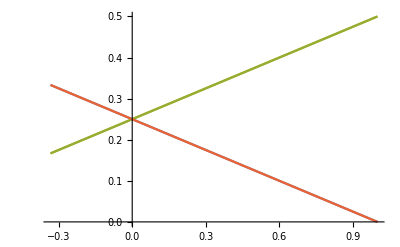

```mathematica
Plot[{Tr[ConjugateTranspose[M00] M00 rho[p]] ,Tr[ConjugateTranspose[M01] M01 rho[p]],Tr[ConjugateTranspose[M10] M10 rho[p]],Tr[ConjugateTranspose[M11] M11 rho[p]]},{p,-0.333,1}]
```

```mathematica
Manipulate
```

```mathematica
st
```

st0

```mathematica
II.Estados no puros de dos qubits y traspuesta parcial
```

```mathematica
7)|ψ>=(|01>-|10>) /√2
```

```mathematica
a)
```

```mathematica
ψ=1/√2. ({{0}, {1}, {-1}, {0}} )
```

{{0.},{0.707107},{-0.707107},{0.}}

```mathematica
ψ.Transpose[ψ]
```

{{0.,0.,0.,0.},{0.,0.5,-0.5,0.},{0.,-0.5,0.5,0.},{0.,0.,0.,0.}}

```mathematica
rho[x_]=x ψ.Transpose[ψ]+(1-x) s1[4,4]/4
```

{{0.+(1-x)/4,0.,0.,0.},{0.,(1-x)/4+0.5 x,-0.5 x,0.},{0.,-0.5 x,(1-x)/4+0.5 x,0.},{0.,0.,0.,0.+(1-x)/4}}

```mathematica
MatrixForm[rho[x]]
```

```mathematica
({{0.+(1-x)/4, 0., 0., 0.}, {0., (1-x)/4+0.4999999999999999 x, -0.4999999999999999 x, 0.}, {0., -0.4999999999999999 x, (1-x)/4+0.4999999999999999 x, 0.}, {0., 0., 0., 0.+(1-x)/4}})
```

```mathematica
Solve[rho[x].rho[x]==rho[x],x]
```

{{x→1.}}

```mathematica
rho[1]
```

{{0.,0.,0.,0.},{0.,0.5,-0.5,0.},{0.,-0.5,0.5,0.},{0.,0.,0.,0.}}

```mathematica
rho[1].rho[1]
```

{{0.,0.,0.,0.},{0.,0.5,-0.5,0.},{0.,-0.5,0.5,0.},{0.,0.,0.,0.}}

```mathematica
Eigenvalues[rho[x]]
```

{0.+(1-x)/4,0.+(1-x)/4,0.5 (0.5-0.5 x),0.5 (0.5+1.5 x)}

```mathematica
Reduce[{(1-x)/4>0,0.5 (0.5-0.5 x)>0,0.5 (0.5+1.4999999999999996 x)>0},x]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

-0.333333<x<1.

```mathematica
Reduce[{((1-x)/4)>0,(0.5-0.5 x)>0,(0.5+1.5 x)>0},x]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

-0.333333<x<1.

```mathematica
rho[x]
```

{{0.+(1-x)/4,0.,0.,0.},{0.,(1-x)/4+0.5 x,-0.5 x,0.},{0.,-0.5 x,(1-x)/4+0.5 x,0.},{0.,0.,0.,0.+(1-x)/4}}

```mathematica
Tr[rho[x]]
```

1.-2.22045×10^-16 x

```mathematica
MatrixForm[ψ.Transpose[ψ]]
```

(0. | 0. | 0. | 0.
0. | 0.5 | -0.5 | 0.
0. | -0.5 | 0.5 | 0.
0. | 0. | 0. | 0.)

```mathematica
10 01 -> 11 00, 01 10->00 11
```

```mathematica
rhotb[x_]=({{(1-x)/4, 0, 0, -0.5 x}, {0, (1-x)/4+0.5 x, 0, 0}, {0, 0, (1-x)/4+0.5 x, 0}, {-0.5 x, 0, 0, (1-x)/4}})
```

{{(1-x)/4,0,0,-0.5 x},{0,(1-x)/4+0.5 x,0,0},{0,0,(1-x)/4+0.5 x,0},{-0.5 x,0,0,(1-x)/4}}

```mathematica
Eigenvalues[{{(1-x)/4,0,0,-0.5 x},{0,(1-x)/4+0.5 x,0,0},{0,0,(1-x)/4+0.5 x,0},{-0.5 x,0,0,(1-x)/4}}]
```

{0.5 (0.5-1.5 x),0.5 (0.5+0.5 x),(1-x)/4+0.5 x,(1-x)/4+0.5 x}

```mathematica
Reduce[((1-x)/4)+0.5 x<0,x]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

x<-1.

```mathematica
Reduce[0.5(0.5-1.5 x)<0,x]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

x>0.333333

```mathematica
Reduce[0.5 (0.5+0.5 x)<0,x]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

x<-1.

```mathematica
rho=p({{Abs[a]^2, a Conjugate[b]}, {Conjugate[a] b, Abs[b]^2}})+(1-p)({{Abs[c]^2, c Conjugate[d]}, {Conjugate[c] d, Abs[d]^2}})
```

{{p Abs[a]^2+(1-p) Abs[c]^2,a p Conjugate[b]+c (1-p) Conjugate[d]},{b p Conjugate[a]+d (1-p) Conjugate[c],p Abs[b]^2+(1-p) Abs[d]^2}}

```mathematica
Tr[rho]
```

p Abs[a]^2+p Abs[b]^2+(1-p) Abs[c]^2+(1-p) Abs[d]^2

```mathematica
(* √q |α\=U11√p |0\+U12√1-p |1\   √1-q |β\=U21√p |0\+U22√1-p |1\ *)
```

```mathematica
U=({{u11, u12}, {u21, u22}});
```

```mathematica
U.ConjugateTranspose[U]
```

{{u11 Conjugate[u11]+u12 Conjugate[u12],u11 Conjugate[u21]+u12 Conjugate[u22]},{u21 Conjugate[u11]+u22 Conjugate[u12],u21 Conjugate[u21]+u22 Conjugate[u22]}}

```mathematica
ConjugateTranspose[U].U
```

{{u11 Conjugate[u11]+u21 Conjugate[u21],u12 Conjugate[u11]+u22 Conjugate[u21]},{u11 Conjugate[u12]+u21 Conjugate[u22],u12 Conjugate[u12]+u22 Conjugate[u22]}}

```mathematica
s1[1].s1[2]
```

{{ⅈ,0},{0,-ⅈ}}

```mathematica
I s1[3]
```

{{ⅈ,0},{0,-ⅈ}}

```mathematica
(rx s1[1]+ry s1[2]+rz s1[3]+ s1[4])/2
```

{{(1+rz)/2,1/2 (rx-ⅈ ry)},{1/2 (rx+ⅈ ry),(1-rz)/2}}

```mathematica
Eigenvalues[{{(1+rz)/2,1/2 (rx-ⅈ ry)},{1/2 (rx+ⅈ ry),(1-rz)/2}}]
```

{1/2 (1-√(rx^2+ry^2+rz^2)),1/2 (1+√(rx^2+ry^2+rz^2))}

```mathematica
Eigensystem[(rx s1[1]+ry s1[2]+rz s1[3]+ s1[4])/2]
```

{{1/2 (1-√(rx^2+ry^2+rz^2)),1/2 (1+√(rx^2+ry^2+rz^2))},{{-(-rz+√(rx^2+ry^2+rz^2))/(rx+ⅈ ry),1},{-(-rz-√(rx^2+ry^2+rz^2))/(rx+ⅈ ry),1}}}

```mathematica
rho1=({{1, 0}, {0, 1}})/2
```

{{1/2,0},{0,1/2}}

```mathematica
Table[Tr[rho1.s1[i]],{i,1,3}]
```

{0,0,0}

```mathematica
rho2=({{2/3, 0}, {0, 1/3}})
```

{{2/3,0},{0,1/3}}

```mathematica
Table[Tr[rho2.s1[i]],{i,1,3}]
```

{0,0,1/3}